Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 4

Metoda predyktor-korektor

Napisać procedurę realizującą algorytm metody predyktor-korektor (argumenty:  f, x_0, y_0, b, n).
Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego. Jako metodę predykcji wykorzystać trzy krokową metodę Adamsa-Bashfortha, a jako metodę korekcji trzy krokową metodę Adamsa-Moultona. W metodzie korekcji wykonać dwie iteracje metody iteracji prostej.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=2 sin x - y(x),  x∈[0,15],
y(0)=2.

Obliczenia wykonać dla 20 i 100 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Wyznaczyć także błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

### Metoda Rungego-Kutty rzędu trzeciego - kod procedury

Wejście: 
	f = f(x,y) - funkcja;
	x0, y0 - wartości;
	n - liczba kroków;
	h - długość kroku.
Wyjście:
	(x_i,y_i) dla i=0,1,...,n - punkty.

```mathematica
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_]:=Module[{xi,yi,xNext=x0,yNext=y0,k1,k2,k3},

xi={x0};
yi={y0};

Do[
(*k1=f[xNext,yNext];
k2=f[xNext+h/2,yNext+(h k1)/2];
xNext=xNext+h;
xi=Append[xi,xNext];
k3=f[xNext,yNext-h k1+2 h k2];
yNext=yNext+1/6 h (k1+4 k2+k3);
yi=Append[yi,yNext],
{i,0,n-1}*)

k1=f[xi⟦i⟧,yi⟦i⟧];
k2=f[xi⟦i⟧+h/2,yi⟦i⟧+(h k1)/2];
xi=Append[xi,xi⟦i⟧+h];
k3=f[xi⟦i+1⟧,yi⟦i⟧-h k1+2 h k2];
yi=Append[yi,yi⟦i⟧+1/6 h (k1+4 k2+k3)];,
{i,1,n}

];

Return[Transpose[{xi,yi}]]
]
```

### Metoda predyktor-korektor

Wejście:
	f - funkcja f = f(x, y),
	x0, y0 - wartości x_0, y_0,
	b - koniec przedziału,
	n - liczba kroków.
Wyjście:
	punkty (x_i, y_i), i = 0, 1, ..., n.

```mathematica
Clear[metodaPK];
metodaPK[f_,x0_,y0_,b_,n_]:=Module[{h=(b-x0)/n,xi,yi,k=3,fi,yInit=0,bki,bbar,nmip=2,temp=0},

bki={23/12,-16/12,5/12};(* indeksowane od 1 *)
bbar={9/24,19/24,-5/24,1/24};(* indeksowane od zera *)

(* Wyznaczamy węzły siatki *)
xi=Table[x0+i*h,{i,k-1}];
xi=Prepend[xi,x0];

(* Metoda startowa *)
yi=metodaRK3[f,x0,y0,h,k-1]⟦All,2⟧;

(* Obliczamy fi *)
fi=Table[f[xi⟦i⟧,yi⟦i⟧],{i,1,k}];

Do[
xi=Append[xi,xi⟦η-1⟧+h];

(* Predykcja: metodaAB *)
yInit=yi⟦η-1⟧+h(bki⟦1⟧ fi⟦η-1⟧+bki⟦2⟧ fi⟦η-2⟧+bki⟦3⟧ fi⟦η-3⟧);

(* Korekta: metodaAM i metoda iteracji prostej *)
temp=yInit;
Do[temp=yi⟦η-1⟧+h (bbar⟦2⟧ fi⟦η-1⟧+bbar⟦3⟧ fi⟦η-2⟧+bbar⟦4⟧ fi⟦η-3⟧)+h bbar⟦1⟧ f[xi⟦η⟧,temp],{nmip}];

yi=Append[yi,temp];
fi=Append[fi,f[xi⟦η⟧,yi⟦η⟧]];,

{η,k+1,n+1}];
Return[Transpose[{xi,yi}]]
]
```

### Rozwiązanie zagadnienia początkowego

```mathematica
Clear[f,x0,y0,b,n,n1];
f[x_,y_]:=2Sin[x]-y;x0=0.;y0=2.;b=15.;n=20;
n1=100;
przyblizone20=metodaPK[f,x0,y0,b,n];
przyblizone100=metodaPK[f,x0,y0,b,n1];
przyblizoneWykres20=ListPlot[przyblizone20,PlotLegends->{"n=20"},PlotStyle->Orange,PlotMarkers->{✶,Large}];
przyblizoneWykres100=ListPlot[przyblizone100,PlotLegends->{"n=100"},PlotStyle->Brown,PlotMarkers->{Automatic,Tiny}];
```

```mathematica
dokladne=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x]⟦1,1,2⟧;
dokladneWykres=Plot[dokladne,{x,0,15},PlotStyle->LightPink,PlotLegends->{"DSolve"}];
```

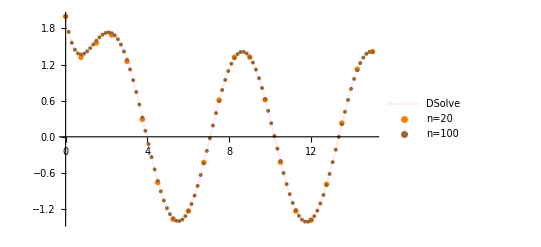

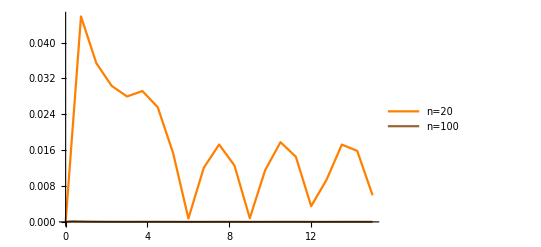

```mathematica
dokladne20=Table[{(x0+(i (b-x0))/n),dokladne/.{x->x0+i (b-x0)/n}},{i,0,n}];
dokladne100=Table[{(x0+(i (b-x0))/n1),dokladne/.{x->x0+i (b-x0)/n1}},{i,0,n1}];
bledy20=Table[{przyblizone20[[i,1]],Abs[przyblizone20[[i,2]]-dokladne20⟦i,2⟧]},{i,Length[dokladne20]}];
bledy100=Table[{przyblizone100[[i,1]],Abs[przyblizone100[[i,2]]-dokladne100⟦i,2⟧]},{i,Length[dokladne100]}];
bledyWykres20=ListPlot[bledy20,PlotStyle->Orange,PlotLegends->{"n=20"},Joined->True,PlotRange->All];
bledyWykres100=ListPlot[bledy100,PlotStyle->Brown,PlotLegends->{"n=100"},Joined->True,PlotRange->All];
Show[dokladneWykres,przyblizoneWykres20,przyblizoneWykres100]
Show[bledyWykres20,bledyWykres100]
```

```mathematica
(* Błędy maksymalne odpowiednio dla n=20 i n=100 *)
{Max[bledy20⟦All,2⟧],Max[bledy100⟦All,2⟧]}
```

{0.0458445,0.000140685}

```mathematica
(* Średnie błędy odpowiednio dla n=20 i n=100 *)
{Mean[bledy20⟦All,2⟧],Mean[bledy100⟦All,2⟧]}
```

{0.0166234,0.0000195709}